Max Gaps.
Todo: redo my discrete sim.  I think the total gap available is m-n -- this should make the math easier.  
There are m-n spaces, which can be placed into n+1 bins.  What is the distribution for the urn with the largest number of spaces?

The number of arrangements is binomial( m-n+n+1 -1,m-n) == binomial(m, m-n)
Uh-oh -- might not have an analytical answer:
http://www.ic.unicamp.br/~celio/peer2peer/math/balls-into-bins.pdf
See also
http://www.nebrija.es/~jmaestro/esa/papers/JDA2011.pdf gives a recurrence relationship (eq 1) . The
new formulation does not require a recursive computation and can be easily implemented
in a symbolic computation tool.

More generally, suppose we have N balls and M bins. Section 9.4 of An Introduction to the Analysis of Algorithms, Second Edition by Robert Sedgewick and Philippe Flajolet shows that the average maximum occupancy is given by
http://math.stackexchange.com/questions/512455/expected-max-load-with-n-balls-in-n-bins
http://ptgmedia.pearsoncmg.com/images/9780321905758/samplepages/032190575X.pdf

```mathematica
(*Formula from http://www.nebrija.es/~jmaestro/esa/papers/JDA2011.pdf, eq 23*)
probHeaviestisb[b_,m_,n_]= ∑_(k=b+1)^n probNbisk[k,m,n]-∑_(k=b+1)^n probNbisk[k+1,m,n]
(*eq 20*)
```

```mathematica
probNbisk[k,m,n] = ck((k!)/m^k)-ckm1(((k-1)!)/m^(k-1))
```

```mathematica
(*eq 18.  
What is z = 1/(1+s/λ)?  
what is v = u/z?
u = λ m t.   where is n? 

Subscript[P, b](n,m) = Probability none of the m buckets has more than b elements, when n elements are distributed randomly
*)
(∑_(j=0)^b (((z/m)^j v^j)/(j!)))^m=∑_(i=0)^b (Subscript[c, i]((z v)/m)^i)
```

```mathematica
Clear[m,c,z,b,v]
FullSimplify[(∑_(j=0)^b (((z/m)^j v^j)/(j!)))^m== ∑_(i=0)^b (c⟦i+1⟧((z v)/m)^i) ]
```

Part::pkspec1: The expression 1 + i cannot be used as a part specification.

((ⅇ^((v z)/m) Gamma[1+b,(v z)/m])/Gamma[1+b])^m==∑_(i=0)^b ((v z)/m)^i c⟦1+i⟧

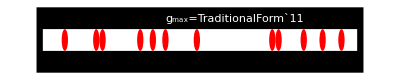

```mathematica
m = 50;
n=12;
d = RandomSample[Range[m],n];
gs = Sort[Join[d,{0,m+1}]];
gi = First[Ordering[Differences[gs],-1]];
Graphics[{
{Black, Rectangle[{0,-1},{m+2,2}]},
{White, Rectangle[{1,0},{m+1,1}]},
{Red,Table[ Disk[{d⟦i⟧+1/2,1/2},1/2],{i,n}]}
,{Opacity[0],Purple,EdgeForm[Directive[Purple,Dashed]],Rectangle[{gs⟦gi⟧+1,1/4},{gs⟦gi+1⟧,3/4}]},
{White,Text[StringForm["g_max=``",gs⟦gi+1⟧-1-gs⟦gi⟧],{(gs⟦gi⟧+1+gs⟦gi+1⟧)/2,1.5}]}
}]
```

```mathematica
Manipulate[
Module[{gs,gi,fi},
If[n>m,n=m;];
If[nold≠ n,redraw=True;nold=n];
If[redraw==True,d = Sort[RandomSample[Range[m],n]];redraw=False];
If[left==True,left=False;
fi=First[FirstPosition[Differences[Prepend[d,0]],x_/;x>1,{0}]];
d⟦fi;;⟧=d⟦fi;;⟧-1;
]; 
If[right==True,right=False;
fi=First[FirstPosition[Differences[Reverse[Append[d,m+1]]],x_/;x<-1,{n+1}]];
d⟦1;;n+1-fi⟧=d⟦1;;n+1-fi⟧+1;
]; 
gs = Sort[Join[d,{0,m+1}]];
gi = First[Ordering[Differences[gs],-1]];
Graphics[{
{Black, Rectangle[{0,-1},{m+2,2}]},
{White, Rectangle[{1,0},{m+1,1}]},
{Red,Table[ Disk[{d⟦i⟧+1/2,1/2},1/2],{i,n}]}
,{Opacity[0],Purple,EdgeForm[Directive[Purple,Dashed]],Rectangle[{gs⟦gi⟧+1,1/4},{gs⟦gi+1⟧,3/4}]},
{White,Text[StringForm["g_max=``",gs⟦gi+1⟧-1-gs⟦gi⟧],{(gs⟦gi⟧+1+gs⟦gi+1⟧)/2,1.5+m/50}]}
},Background->Black,ImageSize->Large]],{{m,20,"m"}, 1,100,1},{{n,10,"n"},1,m,1},
{d,None},{nold,None},
{{redraw,True},None},{left,None},{right,None},
Row[{Button["redraw",redraw=True],
Button["←",left=True,ImageSize->50],Button["→",right=True,ImageSize->50]}]
]
```

```mathematica
dr 
Ordering[Differences[d],-1]
```

{1,2,3,6,7}

{1}

```mathematica
gs
gi
```

{1,2,3,6,7}

{0,4,5,8,9,10,11}

{1}

```mathematica
simMaxSpace[m_,n_]:=Max[Differences[Sort[Join[RandomSample[Range[m],n],{0,m+1}]]]]-1;
m=5;n=0;trials = 10000;
gapProb=Transpose[Table[Rationalize[maxGap = Table[simMaxSpace[m,n],{trials}];N[BinCounts[maxGap,{0,m+2,1}]/trials],.01],{n,0,m}]];
gapProb//MatrixForm 
Total[gapProb,{1}]
```

(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1/10 | 3/5 | 1 | 0
0 | 1/5 | 3/5 | 2/5 | 0 | 0
0 | 2/5 | 3/10 | 0 | 0 | 0
0 | 2/5 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

{1,1,1,1,1,1}

```mathematica
m=5;n=0;
(* THIS ONE IS CLOSE: maxGapCDF[g_,n_,m_]:=Module[{K = Min[n+1,If[g≤ 0,n+1,Floor[(m-n)/g]]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k g/(m+1-n))^n]*)

(*maxGapCDF[g_,n_,m_]:=If[g< (m-n)/(n+1) ,1,Module[{K =Min[n+1,Floor[(m-g)/(g+1)]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k (g+1)/(m-g))^n]]*)
maxGapCDF[g_,n_,m_]:=If[g≤ 0,1,Module[{K = Min[n+1,n+1,Floor[(m-n)/(g+1)]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k (g+1)/(m+1-n))^n]]

d2 = Table[maxGapCDF[g-1,n,m]-maxGapCDF[g,n,m],{g,0,m+1},{n,0,m}]; (*look at columns*)
d2//MatrixForm
Total[d2,{1}]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 | 23/27 | 1 | 1
0 | 1/5 | 9/16 | 4/27 | 0 | 0
0 | 2/5 | 3/16 | 0 | 0 | 0
0 | 2/5 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

{1,1,1,1,1,1}

```mathematica
({{0, 0, 0, 0, 0, 1}, {0, 0, 1/10, 3/5, 1, 0}, {0, 1/5, 3/5, 2/5, 0, 0}, {0, 2/5, 3/10, 0, 0, 0}, {0, 2/5, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}})
```

### m spaces, n robots are placed in positions from 1 to m. We want the distribution for the maximum gap size, or g = max({ x_(1),x_(2)-x_(1),x_(3)-x_(2), ... ,x_(n)-x_(n-1),m+1-x_(n)}) What is the maximum largest gap size? This occurs when all robots are at one end. The max gap is (m+1-n), equivalently (m-n+1) g_max=m+1-n What is the minimum largest gap size? This occurs when robots are evenly distributed and robots are not at the extreme ends (we can assume a ‘robot’ is at 0 and m+1 and there are n+2 robots distributed) , and is g_min=(m-n)/(n+1)+1 no, the minimum largest gap size is when the outside robots are at maximums, and the inside ones are have n-1 gaps of size g g_min=(m-n)/(n+1) if m = 5, the probability distribution is n=0 | 1 | 2 | 3 | 4 | 5 g=0 1 2/1 3/1 4/1 5/1 6(0 | 0 | 0 | 0 | 0 | 0 0 | 0 | 0 | 0 | 0 | 1 0 | 0 | 1/10 | 3/5 | 1 | 0 0 | 1/5 | 3/5 | 2/5 | 0 | 0 0 | 2/5 | 3/10 | 0 | 0 | 0 0 | 2/5 | 0 | 0 | 0 | 0 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
simMaxGap[m_,n_]:=Max[Differences[Sort[Join[RandomSample[Range[m],n],{0,m+1}]]]];
m=5;n=0;
trials = 100000;
gapProb=Transpose[Table[Rationalize[maxGap = Table[simMaxGap[m,n],{trials}];N[BinCounts[maxGap,{0,m+2,1}]/trials],.01],{n,0,m}]];
gapProb//MatrixForm 
Total[gapProb,{1}]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1/10 | 3/5 | 1 | 0
0 | 1/5 | 3/5 | 2/5 | 0 | 0
0 | 2/5 | 3/10 | 0 | 0 | 0
0 | 2/5 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

{1,1,1,1,1,1}

### Sim m = 3

```mathematica
m=3;
trials = 100000;
maxGap = Table[simMaxGap[m,n],{trials}];
gapProb10=Transpose[Table[Rationalize[maxGap = Table[simMaxGap[m,n],{trials}];N[BinCounts[maxGap,{0,m+2,1}]/trials],.001],{n,0,m}]];
gapProb10//MatrixForm 
Total[gapProb10,{1}]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1/3 | 1 | 0
0 | 2/3 | 0 | 0
1 | 0 | 0 | 0)

{1,1,1,1}

### Sim m = 10

```mathematica
m=10;
trials = 100000;
maxGap = Table[simMaxGap[m,n],{trials}];
gapProb10=Transpose[Table[Rationalize[maxGap = Table[simMaxGap[m,n],{trials}];N[BinCounts[maxGap,{0,m+2,1}]/trials],.001],{n,0,m}]];
gapProb10//MatrixForm 
Total[gapProb10,{1}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1/42 | 1/6 | 13/28 | 4/5 | 1 | 0
0 | 0 | 0 | 1/30 | 3/14 | 10/21 | 3/5 | 7/15 | 1/5 | 0 | 0
0 | 0 | 2/31 | 10/33 | 25/58 | 5/14 | 1/5 | 1/15 | 0 | 0 | 0
0 | 0 | 4/15 | 1/3 | 9/38 | 5/42 | 1/30 | 0 | 0 | 0 | 0
0 | 1/5 | 11/41 | 13/66 | 2/21 | 1/41 | 0 | 0 | 0 | 0 | 0
0 | 1/5 | 1/5 | 1/10 | 1/42 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/5 | 2/15 | 1/30 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/5 | 1/15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{1,1,3811/3813,1,1655/1653,1723/1722,1,419/420,1,1,1}

### Analytical

```mathematica
m=5;
n=0;
maxGapCDF[g_,n_,m_]:=If[g≤ (m-n)/(n+1) ,1,Module[{K =Min[n+1,Floor[(m+1-g)/g]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k g/(m+1-n))^n]]
d = Table[maxGapCDF[g,n,m]-maxGapCDF[g+1,n,m],{g,0,m+1}];
d//MatrixForm
```

(0
0
0
0
0
1
0)

```mathematica
({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 1/3, 1, 0}, {0, 2/3, 0, 0}, {1, 0, 0, 0}})
```

```mathematica
∑_(k=1)^1 1
```

1

```mathematica
Binomial[5,0]
```

1

(0 | 0 | 0 | 0
0 | 0 | 1/4 | 1
0 | 1/3 | 3/4 | 0
0 | 2/3 | 0 | 0
1 | 0 | 0 | 0)

{1,1,1,1}

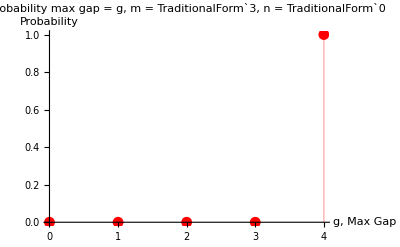

```mathematica
m=3;n=0;
(* THIS ONE IS CLOSE: maxGapCDF[g_,n_,m_]:=Module[{K = Min[n+1,If[g≤ 0,n+1,Floor[(m-n)/g]]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k g/(m+1-n))^n]*)

(*maxGapCDF[g_,n_,m_]:=If[g< (m-n)/(n+1) ,1,Module[{K =Min[n+1,Floor[(m-g)/(g+1)]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k (g+1)/(m-g))^n]]*)
(*maxGapCDF[g_,n_,m_]:=If[g≤ 0,1,Module[{K = Min[n+1,n+1,Floor[(m-n)/(g+1)]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k (g+1)/(m+2-n))^n]]*)
maxGapCDF[g_,n_,m_]:=Module[{K = Min[n+1,If[g≤ 0,n+1,Floor[(m-n)/g]]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k g/(m-n+1))^n]
d2 = Table[maxGapCDF[g-1,n,m]-maxGapCDF[g,n,m],{g,0,m+1},{n,0,m}]; (*look at columns*)(*d = Table[maxGapCDF[g-1,n,m]-maxGapCDF[g,n,m],{g,0,m+1}];d//MatrixForm*)
d2//MatrixForm
Total[d2,{1}]
(* Table[maxGapCDF[g,n,m]-maxGapCDF[g+1,n,m],{g,0,m+1},{n,0,m}]//MatrixForm*)
ListPlot[d,PlotStyle->Red,Filling->Axis,AxesLabel->{"g, Max Gap","Probability"},PlotLabel->StringForm["probability max gap = g, m = ``, n = ``",m,n],PlotRange->All,DataRange->{0,m+1}]
```

Try Harmonic Number for expected value:
http://math.stackexchange.com/questions/14190/average-length-of-the-longest-segment
This overestimates the gap size, but works well for n<<m

```mathematica
expectedMaxGap[m_,n_]:=(m+1)HarmonicNumber[n+1]/(n+1);
simMaxGap[m_,n_]:=Max[Differences[Sort[Join[RandomSample[Range[m],n],{0,m+1}]]]];
```

```mathematica
m=1000;n=1000;trials = 10000;
 N[Mean[Table[simMaxGap[m,n],{trials}]]]

N[expectedMaxGap[m,n]]
```

1.

7.48647

Doesn't work: DiscreteUniformDistribution OrderDistribution because we can’t have repeats

```mathematica
Clear[m,n]
(*problem: we can't have repeats*)
𝒟=OrderDistribution[{OrderDistribution[{DiscreteUniformDistribution[{1,m}],n},1],n},n]
PDF[𝒟,g]
```

OrderDistribution[{OrderDistribution[{DiscreteUniformDistribution[{1,m}],n},1],n},n]

Piecewise[{{(1-(1-g/m)^n)^n-(1-(1+1/m-g/m)^n)^n, g≥1&&g-m<0}, {1-(1-m^-n)^n, g-m==0&&g≥1}, {0, g<1||g-m≥0}, {-(1-(1+1/m)^n)^n, True}}]

```mathematica
maxG[g_,m_,n_]:=(1-(1-g/m)^n)^n-(1-(1+1/m-g/m)^n)^n
m=5;
d2 = Table[maxG[g,m,n],{g,1,m-1},{n,1,m}]; (*look at columns*)
d2//MatrixForm
```

(1/5 | 81/625 | 226981/1953125 | 18539817921/152587890625 | 40938343154110501/298023223876953125
1/5 | 7/25 | 714211/1953125 | 2761531927/6103515625 | 157886149254951931/298023223876953125
1/5 | 37/125 | 660421/1953125 | 9994920013/30517578125 | 84249258755836261/298023223876953125
1/5 | 27/125 | 305011/1953125 | 2812190643/30517578125 | 14472940631991931/298023223876953125)

Might work

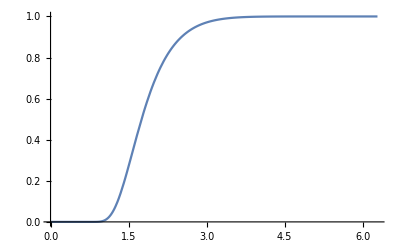

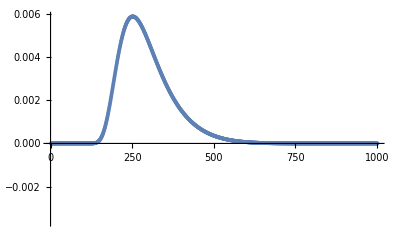

```mathematica
(*http://math.stackexchange.com/questions/18938/maximum-gap-among-n-points-on-a-circle*)
FmaxgapCircle[θ_,N_]:=Module[{K = Min[N,If[θ==0,N,(2π)/θ]]},∑_(k=1)^K (-1)^(k-1)Binomial[N,k](1-k θ/(2 π))^(N-1)]
m=1000;n=10;
Plot[1-FmingapCircle[θ,n],{θ,0,2π}]
cgAcc = ListPlot[Table[-(FmingapCircle[θ,n]-FmingapCircle[θ-2π/m,n]),{θ,0,2π,2π/m}]]
```

```mathematica
Clear[L,k,K,m,n]
probGap1biggerThany[y_,m_,n_]:=If[y>m-n+1,0,1/Binomial[m,n]∑_(k=Max[1,y+1])^(m-n+1) Binomial[m-k,n-1]]
```

```mathematica
(Binomial[m-Max[1,1+y],-1+n] (1+m-Max[1,1+y]))/(n Binomial[m,n])
probGap1biggerThany[y,m,n]
```

```mathematica
(Binomial[m-Max[1,1+y],-1+n] (1+m-Max[1,1+y]))/(n Binomial[m,n])
```

(Binomial[m-Max[1,1+y],-1+n] (1+m-Max[1,1+y]))/(n Binomial[m,n])

```mathematica
probGap1biggerThany[8,5,3]
```

0

```mathematica
Evaluate[Table[probGap1biggerThany[g,m,4],{g,0,m+1}]]
```

{1,1/5,0,0,0,0,0}

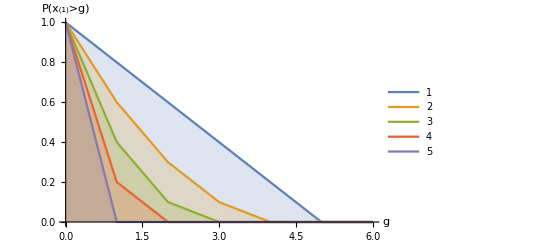

```mathematica
m=5;
ns = {1,2,3,4,5}; 
ts[g_]:=Table[probGap1biggerThany[g,m,n],{n,ns}];
DiscretePlot[Evaluate[ts[g]],{g,0,m+1},Joined->True,PlotLegends->ns,AxesLabel->{"g","P(x_(1)>g)"},PlotRange->All]
```